```mathematica
A=0.8
B=0.2
```

0.8

0.2

```mathematica
f[x_]:=1/(√(A x^-2+B x^-1))
```

```mathematica
F[a_]:=NIntegrate[f[x],{x,0,a}]
```

Solution for 1a

NIntegrate::nlim: x = a is not a valid limit of integration.

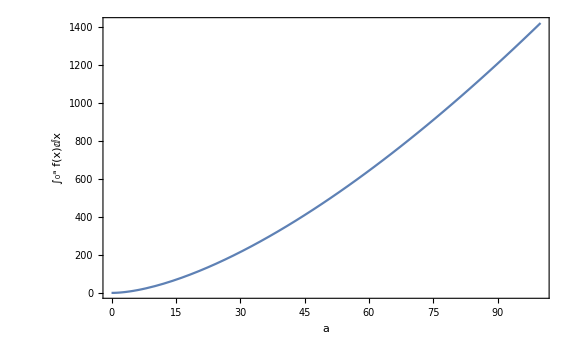

```mathematica
Plot[F[a],{a,0,100},Frame->True,FrameLabel->{"a","∫_0^a f(x)ⅆx"}]
```

For 1b, I’ll make a table of pairs of (a,F[a]), then plot (F[a],a) (i.e. reversing the axes)
In the next two lines below, remove the “;” to see the (very long) output of the Table and Map commands

```mathematica
data= Table[{a,F[a]},{a,0,100,0.1}];
```

```mathematica
reverseddata=Map[{#[[2]],#[[1]]}&,data];
```

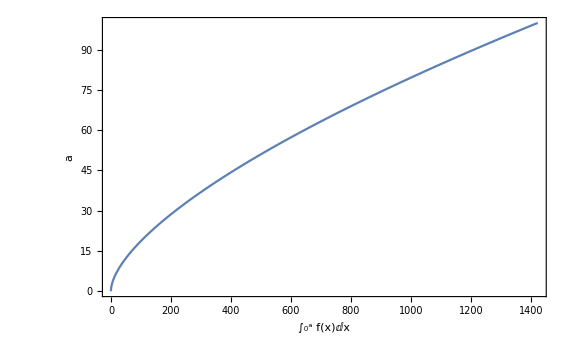

```mathematica
ListPlot[reverseddata,Frame->True,Joined->True,FrameLabel->{"∫_0^a f(x)ⅆx","a"}]
```

For c, there are a couple of ways you can do this. One way is to take the derivative of F with respect to a, then evaluate the result at a particular value of a:

```mathematica
dF[x_]:=D[F[a],a]/.{a->x}
```

The syntax here is D[F[a],a] = “derivative of F with respect to a.” But this results in a function that still has “a” as a variable. Then the “/.” tells mathematica to replace “a” with “x,” where “x” is the variable that the new function of dF[x] will take.

```mathematica
dF[10.]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

5.97614

```mathematica
f[10.]
```

5.97614

NIntegrate::nlim: x = a is not a valid limit of integration.

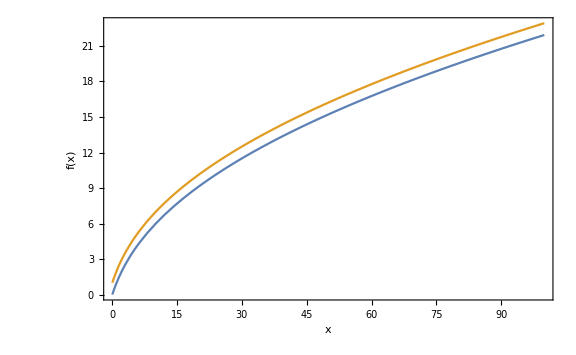

```mathematica
Plot[{f[x],dF[x]+1},{x,0,100},Frame->True,FrameLabel->{"x","f(x)"}]
```